```mathematica
f1[x_?NumericQ]:= mb*x*1/((1+x^2)^(1/2))
f2[x_?NumericQ]:= σ*x^2*1/((1+x^2)^(5/2))
```

```mathematica
DSolve[y'[x] == f1[x]+f2[x]*y[x]^2, y[x], x]
```

DSolve[y'[x]==(mb x)/(√(1+x^2))+(x^2 σ y[x]^2)/((1+x^2)^(5/2)),y[x],x]

```mathematica
f3[x_]:= x*(1+x^2)^(-1/2)
f4[x_]:= σ*x*(1+x^2)^(-3)

DSolve[y'[x] == f3[x]*(mb+f4[x]*y[x]^2), y[x], x]
```

```mathematica
DSolve[y'[x]==(x (mb+(x σ y[x]^2)/((1+x^2)^3)))/(√(1+x^2)),y[x],x]
```

```mathematica
mb := m0 * ab
Msol := 1989*10^(30) 
(*m0 := 10^4*Msol *)
m0 :=1.93943*10^(29)
m0 //N
ab := Rationalize[7.41*10^(-9), 0] (*adimensional*)
ηb := Rationalize[2.19*10^4,0]  (*en segundos*)
ηi := Rationalize[2.96*10^(12),0]   (*en segundos*)
G := 6.674*10^(-8)  (*en cgs*)
c := 2.998*10^(10)   (*en cgs*)
σ :=Rationalize[(81*G)/(8*c^3)*1/(ab*ηb), 0]
xi :=Rationalize[ηi/ηb, 0]
```

1.93943×10^29

```mathematica
m0 :=1.93943*10^(34)
```

```mathematica
dMdx=NDSolve[{y'[x]== mb*x*1/((1+x^2)^(1/2))+σ*x^2*1/((1+x^2)^(5/2))*y[x]^2,y[0]==m0},y,{x,-xi,xi}]
```

{{y→InterpolatingFunction[…]}}

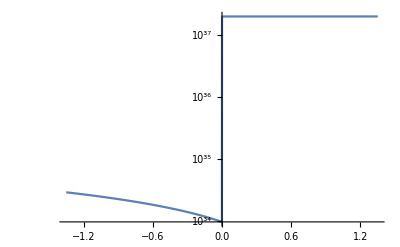

```mathematica
LogPlot[y[x]/.dMdx, {x,-xi,xi},  PlotRange->All]
```

```mathematica
y[100]/.dMdx
```

{1.72598×10^37}

```mathematica
dMdx=NDSolve[{y'[x]==f2[x]*y[x]^2,y[xi]==m0},y,{x,-xi,xi}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
LogPlot[y[x]/.dMdx, {x,-100000,100000},  PlotRange->All]
```

-Graphics-

```mathematica
y[xi]/.dMdx
```

{1.93943×10^29}

```mathematica
y[-xi]/.dMdx
```

{1.93943×10^29}

```mathematica
(*ojooo despues de esto no considerar*)
```

```mathematica
NDSolve::ndnum: "Encountered non-numerical value for a derivative at \!\(\*RowBox[{\"x\"}]\) == \!\(\*RowBox[{\"-\", \"1.3515981735159817`*^8\"}]\)."
```

```mathematica
NDSolve[{y'[x]==(1.4738490000000001*^29 x)/(√(1+x^2))+(1.5453399277928612*^-34 x^2 y[x]^2)/(1+x.b2)^(5/2),y[-1.3515981735159817*^8]==1.989*^37},y,{x,-1.3515981735159817*^8,1.3515981735159817*^8}]
```

```mathematica
Plot[Evaluate[y[x]/. sol],{x,-1,1}]
```

```mathematica
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"sol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
```

```mathematica
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"sol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
```

```mathematica
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"sol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
```

```mathematica
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"ReplaceAll\", \"::\", \"reps\"}], \"MessageName\"]\) will be suppressed during this calculation."
```